## Using Mathematica for combinatorics and probability

In this notebook, we will provide the input cells for the examples -- you should evaluate each input cell to see the outputs. In some cases, later examples may not work if you haven’t evaluated all the previous input cells, so please evaluate each example.

### Using Tuples to enumerate finite sample spaces

You can use Mathematica to count the number of possible outcomes of an experiment that satisfy a certain criterion. For example, suppose you role two six-side dice. You can generate a list all the possible outcomes for this experiment using the built-in function Tuples.

```mathematica
sampleSpace=Tuples[{1, 2, 3, 4, 5, 6}, 2]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6}}

In the output, the first number is the face shown on the first die rolled and the second number is the face shown on the second die. If you’re interested in the probabilities of events when rolling two fair dice then you can assume all possible outcomes are equally likely. Now suppose you are interested in the probability of the event consisting of all possible outcomes in which the sum of the numbers on the two faces is even. First, we need to know how many of the possible outcomes have an even sum. We can pick those outcomes out of the list of all outcomes by using the built-in function Select, which takes a list and a function. It applies the function to each element of the list. For example,

```mathematica
Select[{1, 2, 3, 4, 5}, EvenQ]
```

{2,4}

The return value is a new list consisting of the elements of the original list on which the function returned True. In this case we used the built-in function EvenQ. The Q at the end signifies a query function that tests whether something meets a criterion -- thus, PrimeQ tests whether its argument is a prime number. But for our dice example we can’t use EvenQ directly because we have a list of lists and what we want to know is whether the total of the numbers on the inner list (the die faces) is even. So we need to apply Total before we apply EvenQ. An elegant way to do that is as follows:

```mathematica
evenSumEvent=Select[sampleSpace, EvenQ[Total[#]]&]
```

{{1,1},{1,3},{1,5},{2,2},{2,4},{2,6},{3,1},{3,3},{3,5},{4,2},{4,4},{4,6},{5,1},{5,3},{5,5},{6,2},{6,4},{6,6}}

The expression  EvenQ[Total[#]] & defines a function of one argument that first applies Total to its argument and then applies EvenQ to the result. The # (called sharp) refers to the argument and the & (called ampersand) indicates that the preceding expression should be treated as a function. This is called an anonymous function because it doesn’t have a name -- it is defined just long enough to be used in this one expression. The ampersand is a shorthand notation for Function, which we could have used instead:

```mathematica
evenSumEvent=Select[sampleSpace, Function[EvenQ[Total[#]]]]
```

{{1,1},{1,3},{1,5},{2,2},{2,4},{2,6},{3,1},{3,3},{3,5},{4,2},{4,4},{4,6},{5,1},{5,3},{5,5},{6,2},{6,4},{6,6}}

Mathematica has many of these shorthand symbols and most of them are better forgotten -- they make code unreadable. However, the ampersand and sharp combination is used almost universally for defining anonymous functions. You can also define anonymous functions with more than one argument and you can name the arguments instead of using # if you want, although this is done rarely. See the documentation on Function when you’re ready to learn more about this (but you don’t have to read it now). 

Now all that’s left is to count the number of outcomes in the event and divide by the total number of outcomes. The function Length gives the number of elements in a list:

```mathematica
Length[evenSumEvent]
```

18

```mathematica
Length[sampleSpace]
```

36

```mathematica
probEvenSumEvent = Length[evenSumEvent]/Length[sampleSpace]//N
```

0.5

The // N at the end means that we want to evaluate the built-in function N on the preceding expression, to get its decimal value rather than the fraction that is otherwise returned and we were lazy about it by placing the function name at the end.  We could have used functional syntax like so:

```mathematica
probEvenSumEvent = N[Length[evenSumEvent]/Length[sampleSpace]]
```

0.5

Placing the function at the beginning or end of an expression is a matter of style and readability -- in general, I prefer it at the beginning. However,  functions that modify the output format, e.g., N and MatrixForm, are often written in this postfix notation, perhaps because such output modifiers are often afterthoughts to the main computation.

Did you really need Mathematica to figure out that the probability of getting an even sum when rolling two fair dice is 0.5? Of course not! But here’s a problem that will make you grateful you don’t have to do it by hand.

##### Practice: Using lists to count the number of outcomes in an event

Suppose you are rolling the following dice, each of which has an equal probability of turning up each of its faces: two 4-sided dice, three 6-sided, and one 12-sided. Calculate the probability that the sum of the faces is a prime number.

Here’s how to approach it.

Use Tuples to create a list of all possible outcomes (the sample space). Since your dice are not identical, you’ll have to pass Tuples a list of lists of possible outcomes for the dice. Please read the documentation on Tuples far enough to figure out how to do this. The resulting sample space is big so you will probably want to assign the list representing it to a variable like sampleSpace and put a semi-colon at the end of the line to suppress the printing of the result. If you want to avoid typing in the lists of possible outcomes on each die you can look up and use the function Range, which generates lists of successive integers. Before going on, check the number of outcomes in the sampleSpace by using Length and verify that it is correct.

Select out the outcomes whose sum is prime and assign them to a variable with a name like primeSumEvent. The functions Total and PrimeQ will be handy for this.

Calculate the actual probability of getting a prime sum on these dice

Once you’ve solved this or any other practice problem, please neaten up the notebook, deleting things that you tried along the way but weren’t critical to the final solution, just as you would recopy the essentials from your scratchpaper for a handwritten solution.

```mathematica
d[n_]:=Range[n]
ss=Tuples[{d[4],d[4],d[6],d[6],d[6],d[12]}];
ssL=Length[ss];
pSE=Select[ss,PrimeQ[Total[#]]&];
pSEL=Length[pSE];
prob=pSEL/ssL//N
```

0.264757

### Permutations and Combinations in Mathematica

You can use the built in function Permutations to enumerate all the permutations of a set represented as list. This lists all the permutations of length exactly 3 (see the reference page on Permutations for other ways of using it).

```mathematica
Permutations[{1, 2, 3, 4, 5}, {3}]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,2},{1,3,4},{1,3,5},{1,4,2},{1,4,3},{1,4,5},{1,5,2},{1,5,3},{1,5,4},{2,1,3},{2,1,4},{2,1,5},{2,3,1},{2,3,4},{2,3,5},{2,4,1},{2,4,3},{2,4,5},{2,5,1},{2,5,3},{2,5,4},{3,1,2},{3,1,4},{3,1,5},{3,2,1},{3,2,4},{3,2,5},{3,4,1},{3,4,2},{3,4,5},{3,5,1},{3,5,2},{3,5,4},{4,1,2},{4,1,3},{4,1,5},{4,2,1},{4,2,3},{4,2,5},{4,3,1},{4,3,2},{4,3,5},{4,5,1},{4,5,2},{4,5,3},{5,1,2},{5,1,3},{5,1,4},{5,2,1},{5,2,3},{5,2,4},{5,3,1},{5,3,2},{5,3,4},{5,4,1},{5,4,2},{5,4,3}}

Note that the 3 indicating the number of elements you want in the permutations is actually a list containing the number three, {3}. Built in functions are usually heavily overloaded, meaning they do different things depending on what types of arguments you give them. Sometimes arguments have to appear in a list to communicate exactly what you want done with them. In this case, giving just the number 3 instead of the list {3} as the third argument would produce all permutations of size 3 or less, whereas you want permutations of size exactly three. You couldn’t have guessed this -- you just have to read the documentation on the function.

To get all the combinations of a certain size you can use the function Subsets, which works analogously to Permutations, in that you indicate an exact size by putting the second argument in a list.

```mathematica
Subsets[{1, 2, 3, 4}, {2}]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

Compare the result to the result of calling Permutations with the same arguments:

```mathematica
Permutations[{1, 2, 3, 4}, {2}]
```

{{1,2},{1,3},{1,4},{2,1},{2,3},{2,4},{3,1},{3,2},{3,4},{4,1},{4,2},{4,3}}

In comparing them, think about the following questions. For any two numbers, how many of the pairs in the Subsets output contain them? How many of the pairs in the Permutations output contain them?

### Working with probability distributions

Mathematica knows about a lot of families of probability distributions. One of the simplest is the discrete uniform distribution. For example, DiscreteUniformDistribution[{1,10}] represents the uniform distribution on the integers from 1 to 10 -- the distribution under which all those integers are equally likely to be chosen.

```mathematica
DiscreteUniformDistribution[{1,10}]
```

DiscreteUniformDistribution[{1,10}]

As you can see, it evaluates to itself -- there is no way to simplify or reduce it. It doesn’t do anything until you pass it in to another function, such as RandomVariate. RandomVariate  samples from a distribution, as in

```mathematica
RandomVariate[DiscreteUniformDistribution[{1,10}]]
```

7

This in essence “simulates” a process that follows the distribution you pass in. You can give the number of samples you want as a second argument:

```mathematica
RandomVariate[DiscreteUniformDistribution[{1,10}],5]
```

{6,6,6,4,9}

This gets more interesting and useful when the distribution isn’t uniform. For example, EmpiricalDistribution allows you to specify the probability of each outcome explicitly, as in

```mathematica
ed=EmpiricalDistribution[{.2, .6, .1, .1}->{1, 2, 3, 4}]
```

DataDistribution[«Empirical»,{4}]

Now if we sample from it, we’ll get a lot more 2’s than anything else, then 1’s, and occasional 3’s and 4’s.

```mathematica
data=RandomVariate[ed,100]
```

{2,4,1,2,4,2,2,2,1,1,1,2,3,1,1,3,2,2,1,1,1,2,3,4,1,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,4,2,2,2,3,2,2,4,2,1,2,4,2,2,1,3,1,2,2,2,3,2,2,2,2,3,3,2,1,2,1,2,1,4,2,2,3,2,4,1,2,2,4,2,3,4,2,1,3,2,2,2,3,1,2,3,4,3,1}

You can also just pass in a list and it will use the frequencies from the list to generate an empirical distribution:

```mathematica
ed2=EmpiricalDistribution[data]
```

DataDistribution[«Empirical»,{100}]

Here’s an example of sampling approximate reals from a continuous distribution -- the normal (Gaussian) distribution with mean 5 and standard deviation 2:

```mathematica
RandomVariate[NormalDistribution[5, 2], 20]
```

{6.45299,9.50775,4.70876,2.95321,5.77048,9.6873,5.27311,3.91885,6.64948,6.02528,5.17456,5.63875,3.33759,4.23599,1.34237,2.76761,5.56915,7.93514,1.81196,9.25591}

We can plot a histogram of a larger sample to see the familiar “bell curve” shape:

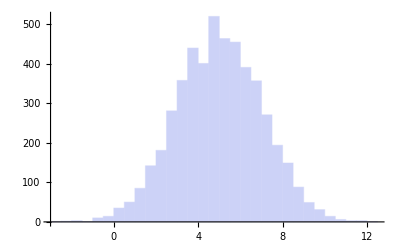

```mathematica
Histogram[RandomVariate[NormalDistribution[5, 2], 5000]]
```

That was a plot of a sample, but we can also plot the distribution itself:

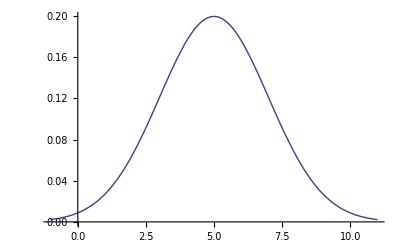

```mathematica
Plot[PDF[NormalDistribution[5, 2], x],{x, -1, 11}]
```

The function PDF (for “probability density function”) gives the probability density at a particular point. For example,

```mathematica
PDF[NormalDistribution[5, 2], 7]
```

1/(2 √(2 ⅇ π))

This gives the probability density at 7 as an exact real. To get an approximate decimal, use N:

```mathematica
N[PDF[NormalDistribution[5, 2], 7]]
```

0.120985

The second argument to Plot, {x, -1, 11}, indicates that the x in the first argument should be varied from -1 to 11.

##### Practice: Plotting samples and probability distributions

Use BinomialDistribution to simulate the number of heads produced in 10 tosses of a coin with probability 0.8 of producing a heads on each flip (called a success).

Plot a histogram of the numbers of heads produced in 1,000 such experiments.

Plot the actual probability function of the binomial distribution with these parameters, from 0 to 10. The only values with non-zero probability are the integers from 0 to 10, so will want to use DiscretePlot instead of Plot for this.

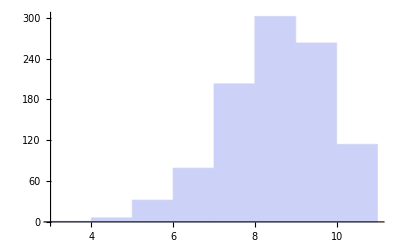

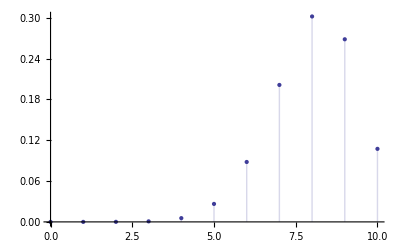

```mathematica
Histogram[RandomVariate[BinomialDistribution[10,0.8],1000]]
DiscretePlot[PDF[BinomialDistribution[10,0.8],x],{x,0,10}]
```

#### Calculating the probabilities of events

When working with probability distributions, often you will want to know the cumulative distribution function (CDF) rather than the probability density function (PDF). For a discrete random variable, the CDF evaluated at some number x is the sum of the probabilities of all numbers less than or equal to x. For a continuous random variable, it is the integral of the PDF from -∞ to x. Mathematica will provide CDF for any distribution it knows:

```mathematica
N[CDF[NormalDistribution[5, 2], 7]]
N[PDF[NormalDistribution[5, 2], 7]]
```

0.841345

0.120985

This is the probability of selecting a number less than or equal 7 from the specified distribution. Notice how different it is than the PDF of the same distribution evaluated at 7. We can also plot the CDF, which always ranges from 0 to 1:

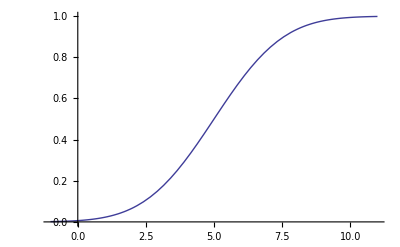

-Graphics-

```mathematica
Plot[CDF[NormalDistribution[5, 2], x],{x, -1, 11}]
Plot[PDF[NormalDistribution[5, 2], x],{x, -1, 11}]
```

Compare this to the PDF we graphed for the same function above. You can see that the CDF rises steeply where the PDF is high and slowly where the PDF is low. This is because the PDF is the derivative of the CDF.

##### Practice: Cumulative Probability Distributions

Use DiscretePlot and CDF to plot the cumulative distribution function of the binomial distribution for 10 tosses of a coin with probability 0.8 of producing a heads. Compare to your plot of the probability function for the same distribution. To make the y-axes comparable, you may want to add the following option to DiscretePlot: PlotRange -> {0, 1}. Options like this are like optional arguments to the function -- they go after all the other arguments, separated by commas. See documentation on Plot for examples.

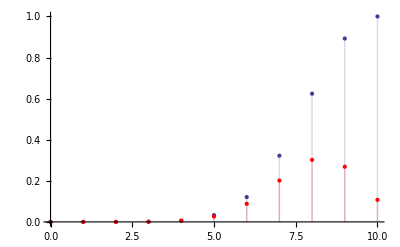

```mathematica
Show[DiscretePlot[CDF[BinomialDistribution[10,0.8],x],{x,0,10}],
DiscretePlot[PDF[BinomialDistribution[10,0.8],x],{x,0,10},PlotStyle->Red]]
```

Now plot the CDF for the tosses of a coin with probability 0.7 of producing heads. Now try 0.6. Write a comment on what happens as you decrease the probability of heads. To make the graphs comparable, you may want to add the following option to DiscretePlot: PlotRange -> {0, 1}.

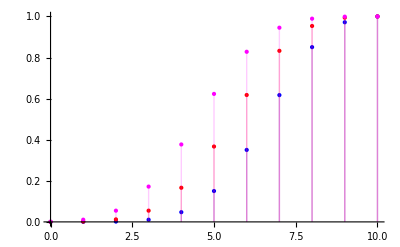

```mathematica
Show[
DiscretePlot[CDF[BinomialDistribution[10,0.7],x],{x,0,10},PlotStyle->Blue],
DiscretePlot[CDF[BinomialDistribution[10,0.6],x],{x,0,10},PlotStyle->Red],
DiscretePlot[CDF[BinomialDistribution[10,0.5],x],{x,0,10},PlotStyle->Magenta]
](*As the probability of a heads decreases, the CDF*)
```

You can use the CDF to calculate the probability of a number sampled from the distribution falling in a certain interval. For example, the probability of a number being between 3 and 7 is simply the probability of its being below 7 minus the probability of its being below 3. That is, the value of the CDF at 7 minus the value of the CDF at 3.

```mathematica
N[CDF[NormalDistribution[5, 2], 7]] - N[CDF[NormalDistribution[5, 2], 3]]
```

0.682689

But you don’t actually have to subtract the CDF values explicitly -- Mathematica does this and much more with the function Probability.

```mathematica
N[Probability[z<7,z \[Distributed] NormalDistribution[5, 2]]]
```

0.841345

```mathematica
N[Probability[3<z<7,z \[Distributed] NormalDistribution[5, 2]]]
```

0.682689

Notice that these are the same numbers we got by using CDF. The first argument to Probability is a predicate -- something that evaluates to True or False -- involving an undefined variable. The second argument gives the distribution of that variable. The little squiggle, \[Distributed], is read “is distributed according to” and can be obtained by typing the escape key, “dist”, and escape again. What’s cool about Probability is that you can give it complicated predicates, as in

```mathematica
N[Probability[2<Sqrt[z] && z^3<125,z \[Distributed] NormalDistribution[5, 2]]]
```

0.191462

```mathematica
Clear["Global`*"]
```

This gives the probability of selecting a number whose square root is greater than two and whose cube is less than 125. By using && (and) and || (or) you can make very complex predicates to calculate the probability of. One thing to beware of is that if you try this with a variable that has a defined value Mathematica will simply replace it by its value before evaluating the rest of the expression. This doesn’t do what you want -- it usually returns a probably of 1 or 0, depending on whether the value of the variable does or does not satisfy your predicate. So you want to make sure your variable is colored blue, indicating undefined, when you use Probability.

If you’re interested in getting out decimal numbers rather than big symbolic expressions, you can use the function NProbability, which in some cases may be faster than computing a symbolic expression for the probability first and then passing it to N.

##### Practice: Using Probability

Suppose you “flip a coin” that has probability 0.75 of producing heads 20 times and add up the number of heads actually produced. You then square that number. Use Probability to figure out the probability that the result will lie in the interval between 20 and 100.

```mathematica
NProbability[20≤z^2≤100,z\[Distributed]BinomialDistribution[20,.75]]
```

0.013864